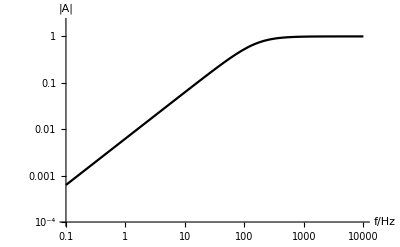

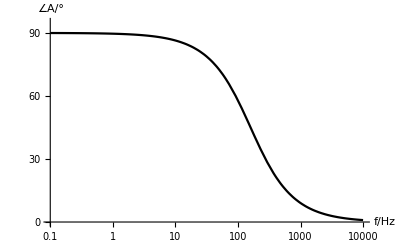

```mathematica
Cc=10^-6;R=1000;
ff[ω_]:=(ⅈ ω Cc R)/(1+ⅈ ω Cc R);
xTicks={0.01,0.1,1,10,100,10^3,10^4};
afTicks={xTicks,{0.0001,0.001,0.01,0.1,1}};
af=LogLogPlot[Abs[ff[2 π f]],{f,0.1,10000},PlotTheme->"Monochrome",PlotRange->{0.0001,2},AxesLabel->{"f/Hz","|A|"}]
pfTicks={xTicks,{90,75,60,45,30,15,0}};
pf=LogLinearPlot[Arg[ff[2 π f]]*180/π,{f,0.1,10000},PlotTheme->"Monochrome",Ticks->{Automatic,{90,75,60,45,30,15,0}}, PlotRange->{0,95},AxesLabel->{"f/Hz","∠A/°"}]
(*GraphicsColumn[{af,pf}]*)
```